## Effective Potential with metrics

{r→6.92598}

-2.03178

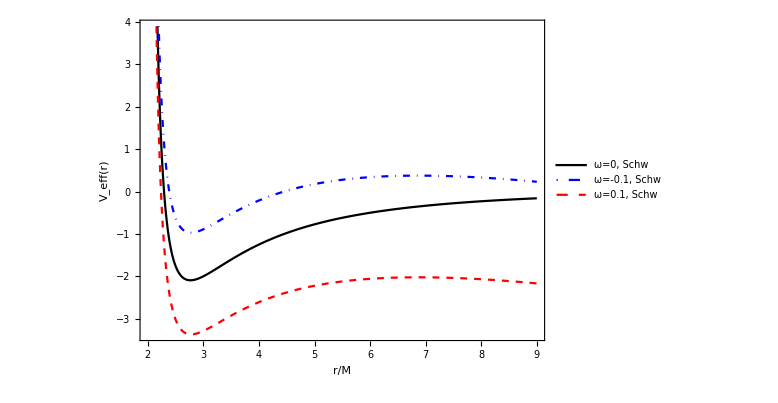

```mathematica
f[r_,Ω_,γ_] = 1 - 2/r(1+Ω/r^2+(Ω γ)/r^3)^-1;
Veff[r_,L_,Ene_,ω_,Ω_,γ_] = -1 + Ene^2/f[r,Ω,γ] - ((L + ω r^2)^2)/r^2; (*ω = eB/(2mc)*)

veff[r_,L_,ω_,Ω_,γ_] = f[r,Ω,γ] (1 + ((L+ ω r^2)^2)/r^2);
FindRoot[D[Veff[r,6,1,0.1,0.6,0.6],r]==0,{r,16}]

Veff[6.925,6,1,0.1,0.6,0.6]
Plot[{Veff[r,6,1,0,0,0],Veff[r,6,1,-0.1,0,0],Veff[r,6,1,0.1,0,0]},{r,2,9},FrameLabel->{"r/M","V_eff(r)","E/M=1, L/M=6"},Frame->True,FrameStyle->Black,AspectRatio->0.7,LabelStyle->Directive[FontFamily->"Times",FontSize->15,Black, Italic,FontColor->Black],ImageSize->Large,PlotLegends->Placed[{"ω=0, Schw","ω=-0.1, Schw","ω=0.1, Schw"},{Scaled[{0.60,0.7}],{0,0.5}}],PlotStyle->{Black,{Blue,DotDashed},{Red,Dashed}}]
```

## Angular momentum and energy

### Energy of charged particle

{r→6.}

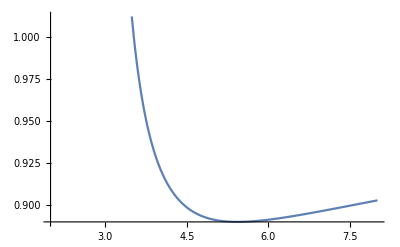

```mathematica
f[r_,Ω_,γ_] = 1 - 2/r(1+Ω/r^2+(Ω γ)/r^3)^-1;
k[r_,Ω_,γ_,ω_]=-((r^4 (r^3-r Ω-2 γ Ω) (-ω+√(1/(r^4 (r^3-r Ω-2 γ Ω)^2)(-4 r^11 ω^2+r^12 ω^2+4 r^10 ω^2 (1+Ω)+r^9 (1+4 (-3+γ) ω^2 Ω)-2 r^2 γ Ω^3 (2+2 γ^2 ω^2-3 γ ω^2 Ω)+γ^3 Ω^3 (-2+γ ω^2 Ω)+r γ^2 Ω^3 (-5+4 γ ω^2 Ω)+2 r^6 Ω (1+ω^2 Ω (2-12 γ+3 γ^2+2 Ω))+r^7 Ω (1-12 ω^2 Ω+4 γ ω^2 (2+3 Ω))+r^8 (-3+2 ω^2 Ω (4-6 γ+3 Ω))+r^4 Ω^2 (1+ω^2 Ω^2+4 γ^2 ω^2 (1+3 Ω)-4 γ (1+3 ω^2 Ω))+r^5 Ω (6 γ-12 γ^2 ω^2 Ω+4 γ ω^2 Ω (2+3 Ω)-Ω (1+4 ω^2 Ω))+r^3 Ω^2 (-Ω+4 γ^3 ω^2 Ω-3 γ^2 (1+4 ω^2 Ω)+γ (2+4 ω^2 Ω^2))))))/(-3 r^5+r^6+2 r^4 Ω+r^3 (-1+2 γ) Ω+r^2 Ω^2+2 r γ Ω^2+γ^2 Ω^2));
Ene[r_,Ω_,γ_,ω_] = (f[r,Ω,γ] (1+((k[r,Ω,γ,ω] + ω r^2)^2)/r^2))^0.5;

 FindRoot[D[Ene[r,0.,0,0.0],r]==0,{r,6}]
Plot[Ene[r,0.1,0,0.02],{r,2,8}]
```

### Angular Momentum

```mathematica
f[r_,Ω_,γ_] = 1 - 2/r(1+Ω/r^2+(Ω γ)/r^3)^-1;

Plot[L[-0.1,0.4,0.2,r]^2,{r,1.5,4}];
```

```mathematica
Solve[D[Veff[r,L,Ene,ω,Ω,γ],r]==0,Ene];
```

```mathematica
ee = -((ⅈ √2 √(L^2-r^4 ω^2))/(r^(3/2) √((4 Ω)/(r^4 (1+Ω/r^2+(γ Ω)/r^3)^2 (1-2/(r (1+Ω/r^2+(γ Ω)/r^3)))^2)+(6 γ Ω)/(r^5 (1+Ω/r^2+(γ Ω)/r^3)^2 (1-2/(r (1+Ω/r^2+(γ Ω)/r^3)))^2)-2/(r^2 (1+Ω/r^2+(γ Ω)/r^3) (1-2/(r (1+Ω/r^2+(γ Ω)/r^3)))^2))));
Solve[-1 + ee^2/f[r,Ω,γ] - ((L + ω r^2)^2)/r^2==0,L];//Simplify
```

```mathematica
k[r_,Ω_,γ_,ω_]=-((r^4 (r^3-r Ω-2 γ Ω) (-ω+√(1/(r^4 (r^3-r Ω-2 γ Ω)^2)(-4 r^11 ω^2+r^12 ω^2+4 r^10 ω^2 (1+Ω)+r^9 (1+4 (-3+γ) ω^2 Ω)-2 r^2 γ Ω^3 (2+2 γ^2 ω^2-3 γ ω^2 Ω)+γ^3 Ω^3 (-2+γ ω^2 Ω)+r γ^2 Ω^3 (-5+4 γ ω^2 Ω)+2 r^6 Ω (1+ω^2 Ω (2-12 γ+3 γ^2+2 Ω))+r^7 Ω (1-12 ω^2 Ω+4 γ ω^2 (2+3 Ω))+r^8 (-3+2 ω^2 Ω (4-6 γ+3 Ω))+r^4 Ω^2 (1+ω^2 Ω^2+4 γ^2 ω^2 (1+3 Ω)-4 γ (1+3 ω^2 Ω))+r^5 Ω (6 γ-12 γ^2 ω^2 Ω+4 γ ω^2 Ω (2+3 Ω)-Ω (1+4 ω^2 Ω))+r^3 Ω^2 (-Ω+4 γ^3 ω^2 Ω-3 γ^2 (1+4 ω^2 Ω)+γ (2+4 ω^2 Ω^2))))))/(-3 r^5+r^6+2 r^4 Ω+r^3 (-1+2 γ) Ω+r^2 Ω^2+2 r γ Ω^2+γ^2 Ω^2));
FindRoot[D[k[r,0,0,0],r]==0,{r,6}]
gg = Table[γ,{γ,0,0.65,0.001}];
rr = Table[r/.FindRoot[(D[k[r,0.1,γ,0.1],r]/.{γ->gg[[i]]})==0,{r,6}],{i,1,Length[gg]}];
rrgg = Table[{gg[[i]],rr[[i]]},{i,1,Length[gg]}];
ListLinePlot[rrgg,Frame->True,FrameLabel->{"γ","r_ISCO/M"},LabelStyle->Directive[FontFamily->"Times",FontSize->14,FontColor->Black],ImageSize->Large];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{r→6.}

## ISCO radii

FindRoot::nlnum: The function value {-(23328. (216.-6. Ω-2. γ Ω) ((0.000771605 (1.69305×10^9 Power[«2»]+4.03108×10^8 Power[«2»] Plus[«2»]+«8»+6480. Ω Plus[«4»]+«1»))/(216.+Times[«2»]+Times[«3»])^2-(0.00154321 «1» («1»))/(«1»)^3-(0.000514403 («1»))/(216.+«1»+Times[«3»])^2))/((23328.+2592. Ω+216. (-1.+Times[«2»]) Ω+36. Ω^2+12. γ Ω^2+γ^2 Ω^2) √((7.25594×10^8 Power[«2»]+2.41865×10^8 Power[«2»] Plus[«2»]+«8»+1296. Power[«2»] Plus[«4»]+«2»)/(216.+Times[«2»]+Times[«3»])^2))+(«1»)/(«1»)-(«1»)/(«1»)-(864. (216.-6. Ω-2. γ Ω) («1»))/(23328.+2592. Ω+«1»+«1»+12. γ Ω^2+γ^2 Ω^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,Ω,γ,ω]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(23328. (216.-6. Ω-2. γ Ω) ((0.000771605 (1.69305×10^9 Power[«2»]+4.03108×10^8 Power[«2»] Plus[«2»]+«8»+6480. Ω Plus[«4»]+«1»))/(216.+Times[«2»]+Times[«3»])^2-(0.00154321 «1» («1»))/(«1»)^3-(0.000514403 («1»))/(216.+«1»+Times[«3»])^2))/((23328.+2592. Ω+216. (-1.+Times[«2»]) Ω+36. Ω^2+12. γ Ω^2+γ^2 Ω^2) √((7.25594×10^8 Power[«2»]+2.41865×10^8 Power[«2»] Plus[«2»]+«8»+1296. Power[«2»] Plus[«4»]+«2»)/(216.+Times[«2»]+Times[«3»])^2))+(«1»)/(«1»)-(«1»)/(«1»)-(864. (216.-6. Ω-2. γ Ω) («1»))/(23328.+2592. Ω+«1»+«1»+12. γ Ω^2+γ^2 Ω^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,Ω,γ,ω]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

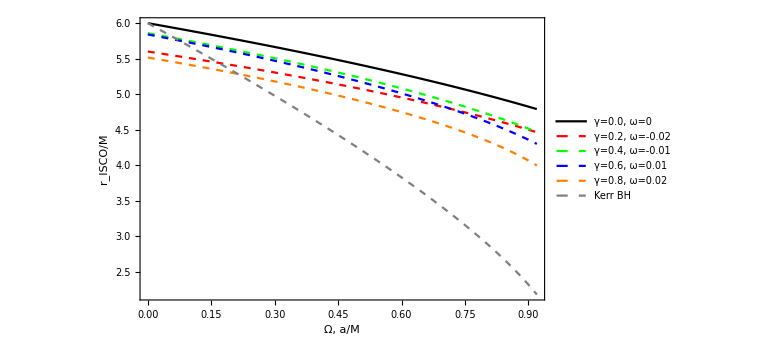

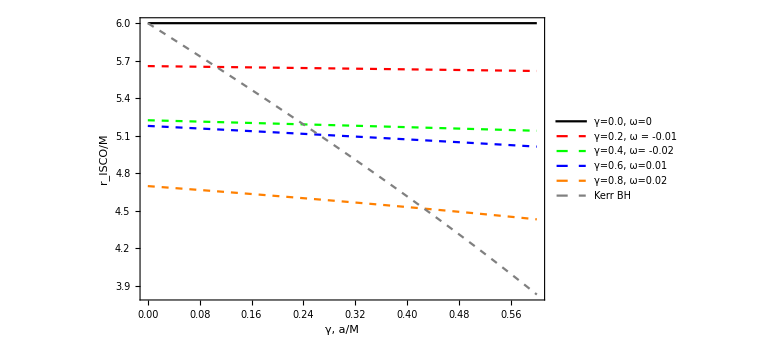

```mathematica
k[r_,Ω_,γ_,ω_]=-((r^4 (r^3-r Ω-2 γ Ω) (-ω+√(1/(r^4 (r^3-r Ω-2 γ Ω)^2)(-4 r^11 ω^2+r^12 ω^2+4 r^10 ω^2 (1+Ω)+r^9 (1+4 (-3+γ) ω^2 Ω)-2 r^2 γ Ω^3 (2+2 γ^2 ω^2-3 γ ω^2 Ω)+γ^3 Ω^3 (-2+γ ω^2 Ω)+r γ^2 Ω^3 (-5+4 γ ω^2 Ω)+2 r^6 Ω (1+ω^2 Ω (2-12 γ+3 γ^2+2 Ω))+r^7 Ω (1-12 ω^2 Ω+4 γ ω^2 (2+3 Ω))+r^8 (-3+2 ω^2 Ω (4-6 γ+3 Ω))+r^4 Ω^2 (1+ω^2 Ω^2+4 γ^2 ω^2 (1+3 Ω)-4 γ (1+3 ω^2 Ω))+r^5 Ω (6 γ-12 γ^2 ω^2 Ω+4 γ ω^2 Ω (2+3 Ω)-Ω (1+4 ω^2 Ω))+r^3 Ω^2 (-Ω+4 γ^3 ω^2 Ω-3 γ^2 (1+4 ω^2 Ω)+γ (2+4 ω^2 Ω^2))))))/(-3 r^5+r^6+2 r^4 Ω+r^3 (-1+2 γ) Ω+r^2 Ω^2+2 r γ Ω^2+γ^2 Ω^2));
rr[Ω_,γ_,ω_]=r/.FindRoot[D[k[r,Ω,γ,ω],r]==0,{r,6.}];
z1 =1+(1-Ω^2)^(1/3)((1+Ω)^(1/3)+(1-Ω)^(1/3));
z2 = Sqrt[3 Ω^2 + z1^2];
rk[Ω_]= 3+z2-Sqrt[(3-z1)(3+z1+2 z2)];       (*  Kerr - ISCO ! *)
Plot[rk[Ω],{a,0,0.5}];
Plot[{rr[Ω,0,0],rr[Ω,0.2,-0.02],rr[Ω,0.4,-0.01],rr[Ω,0.6,0.01],rr[Ω,0.75,0.02],rk[Ω]},{Ω,0.,0.92},Frame->True,FrameLabel->{"Ω, a/M","r_ISCO/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"γ=0.0, ω=0","γ=0.2, ω=-0.02","γ=0.4, ω=-0.01","γ=0.6, ω=0.01","γ=0.8, ω=0.02","Kerr BH"},{Scaled[{0.05,0.15}],{-0.8,0.3}}],PlotStyle->{{Black},{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed, Orange},{Dashed,Gray}},ImageSize->Large]

Plot[{rr[0,γ,0.0],rr[0.2,γ,-0.01],rr[0.4,γ,-0.02],rr[0.6,γ,0.01],rr[0.8,γ,0.02],rk[γ]},{γ,0.,0.6},Frame->True,FrameLabel->{"γ, a/M","r_ISCO/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"γ=0.0, ω=0","γ=0.2, ω = -0.01","γ=0.4, ω= -0.02","γ=0.6, ω=0.01","γ=0.8, ω=0.02","Kerr BH"},{Scaled[{0.05,0.15}],{-0.8,0.3}}],PlotStyle->{{Black},{Dashed,Red},{Dashed,Green},{Dashed,Blue},{Dashed, Orange},{Dashed,Gray}},ImageSize->Large]
```

### Degeneracy plots between Kerr Bh and RGI bh.

FindRoot::nlnum: The function value {(1296. (216.-6. Ω) (27216.+1620. Ω+12. Ω^2) (-0.01+0.0277778 √(Power[«2»] Plus[«9»])))/((23328.+2376. Ω+36. Ω^2)^2)-(864. («1») (-0.01+«21» √(Power[«1»] «1»)))/(23328.+2376. Ω+36. Ω^2)-(«1»)/(«1»)-(23328. (216.-6. Ω) (-(0.000514403 (72559.4+1.00777×10^7 Plus[«2»]+«6»+1.67962×10^6 Plus[«2»]))/(216.+Times[«2»])^2-(«22» «1»«1»(«11»+«7»+«1»))/(«1»)^3+(0.000771605 («1»))/(216.+«1»)^2))/((23328.+2376. Ω+36. Ω^2) √((72559.4+1.00777×10^7 Plus[«2»]+«5»+93312. Ω Plus[«2»]+1.67962×10^6 Plus[«2»])/(216.+Times[«2»])^2))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,Ω,0,0.01]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(1296. (216.-6. Ω) (27216.+1620. Ω+12. Ω^2) (-0.01+0.0277778 √(Power[«2»] Plus[«9»])))/((23328.+2376. Ω+36. Ω^2)^2)-(864. («1») (-0.01+«21» √(Power[«1»] «1»)))/(23328.+2376. Ω+36. Ω^2)-(«1»)/(«1»)-(23328. (216.-6. Ω) (-(0.000514403 (72559.4+1.00777×10^7 Plus[«2»]+«6»+1.67962×10^6 Plus[«2»]))/(216.+Times[«2»])^2-(«22» «1»«1»(«11»+«7»+«1»))/(«1»)^3+(0.000771605 («1»))/(216.+«1»)^2))/((23328.+2376. Ω+36. Ω^2) √((72559.4+1.00777×10^7 Plus[«2»]+«5»+93312. Ω Plus[«2»]+1.67962×10^6 Plus[«2»])/(216.+Times[«2»])^2))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,Ω,0,0.01]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(23328. (216.-6.8 Ω) ((0.000771605 (169305.+«9»+6480. Ω Plus[«4»]+«1»))/(216.+Times[«2»])^2-(0.000514403 (72559.4+«10»+«2»))/(216.+Times[«1»])^2-(0.00154321 (108.-1. Ω) (72559.4+«10»+«2»))/(216.+Times[«2»])^3))/((23328.+2548.8 Ω+40.96 Ω^2) √((72559.4+1.00777×10^7 Plus[«2»]-28.8 Plus[«2»] Power[«2»]+«5»+1.67962×10^6 Plus[«2»]+279936. Ω Plus[«3»]+«2»)/(216.+Times[«2»])^2))+(1296. «2» («1»))/(«1»)^2-(«1»)/(«1»)-(1296. («5»-«1») (-0.01+0.0277778 √(Power[«2»] «1»)))/(23328.+2548.8 Ω+40.96 Ω^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_r k[r,Ω,0.4,0.01]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

FindRoot::nlnum: The function value {(1296. (216.-6. Ω) (27216.+1620. Ω+12. Ω^2) (-0.01+0.0277778 √(Power[«2»] Plus[«9»])))/((23328.+2376. Ω+36. («1»)^2)^2)-(864. («5»-«1») (-0.01+«21» √(«1» «1»)))/(23328.+2376. Ω+36. («1»)^2)-(«1»)/(«1»)-(23328. (216.-6. Ω) (-(0.000514403 (72559.4+1.00777×10^7 Plus[«2»]+«6»+1.67962×10^6 Plus[«2»]))/(216.+Times[«2»])^2-(«22» («1») («1»))/(«1»)^3+(0.000771605 («12»+«7»+«1»))/(216.+«1»)^2))/((23328.+2376. Ω+36. («1»)^2) √((72559.4+1.00777×10^7 Plus[«2»]+«5»+93312. «1» Plus[«2»]+1.67962×10^6 Plus[«2»])/(216.+Times[«2»])^2))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,Ω,0,0.01]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(23328. (216.-6.8 Ω) ((0.000771605 (169305.+«9»+6480. «1» Plus[«4»]+«1»))/(216.+Times[«2»])^2-(0.000514403 («1»))/(«1»)^2-(0.00154321 (108.-1. «1») (72559.4+«10»+«2»))/(216.+Times[«2»])^3))/((23328.+2548.8 Ω+40.96 («1»)^2) √((72559.4+«9»+279936. «1» Plus[«3»]+«2»)/(216.+Times[«2»])^2))+(1296. «2» (-0.01+0.0277778 √(Power[«1»] «1»)))/((23328.+«1»+40.96 («1»)^2)^2)-(«1»)/(«1»)-(1296. (108.-1. Ω) (-0.01+0.0277778 √(Power[«2»] Plus[«12»])))/(23328.+2548.8 Ω+40.96 («1»)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,Ω,0.4,0.01]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(23328. (216.-7.6 Ω) ((0.000771605 (169305.+«9»+6480. «1» Plus[«4»]+«1»))/(216.+Times[«2»])^2-(0.000514403 («1»))/(«1»)^2-(0.00154321 (108.-1. «1») (72559.4+«10»+«2»))/(216.+Times[«2»])^3))/((23328.+2721.6 Ω+46.24 («1»)^2) √((72559.4+1.00777×10^7 Plus[«2»]-57.6 Plus[«2»] Power[«2»]+«6»+279936. «1» Plus[«3»]+«2»)/(216.+Times[«2»])^2))+(1296. («1») «1» (-0.01+«21» √(«1»)))/(«1»)^2-(864. «1»«1»(«1»))/(«1»)-(1296. (108.-1. Ω) (-0.01+0.0277778 √(Power[«2»] Plus[«12»])))/(23328.+2721.6 Ω+46.24 («1»)^2)} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_r k[r,Ω,0.8,0.01]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

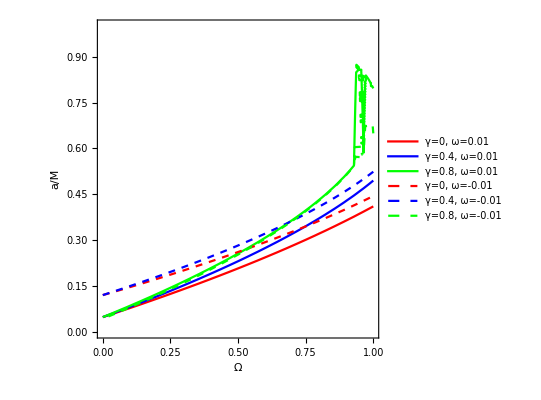

FindRoot::nlnum: The function value {(36. (214.2-0.6 γ) (27735.5+0.18 γ+32.4 (-1.+2. γ)) √((5.15082×10^6+116.64 Plus[«2»]-3.888 γ-0.81 «1»-0.054 Power[«2»]+2332.8 Plus[«2»]+19.44 Plus[«3»])/(214.2+Times[«2»])^2))/((24108.8+1.08 γ+0.09 γ^2+64.8 (-1.+Times[«2»]))^2)-(3877.2 √(«1»))/(24108.8+«1»«1»«1»+64.8 («1»))-(«1»)/(«1»)-(23328. («1») ((0.000771605 (8.52405×10^6+«6»+9.72 Plus[«1»]))/(214.2+Times[«2»])^2-(«19»«1»«1»)/(«1»)^3-(0.000514403«1»«1»)/(«1»)^2))/((24108.8+1.08 γ+0.09 γ^2+64.8 (-1.+Times[«2»])) √((5.15082×10^6+«9»)/(214.2+«1»)^2))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,0.3,γ,0]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {(36. (214.2-0.6 γ) (27735.5+0.18 γ+32.4 (-1.+2. γ)) √((5.15082×10^6+116.64 Plus[«2»]-3.888 γ-0.81 «1»-0.054 Power[«2»]+2332.8 Plus[«2»]+19.44 Plus[«3»])/(214.2+Times[«2»])^2))/((24108.8+1.08 γ+0.09 γ^2+64.8 (-1.+Times[«2»]))^2)-(3877.2 √(«1»))/(24108.8+«1»«1»«1»+64.8 («1»))-(«1»)/(«1»)-(23328. («1») ((0.000771605 (8.52405×10^6+«6»+9.72 Plus[«1»]))/(214.2+Times[«2»])^2-(«19»«1»«1»)/(«1»)^3-(0.000514403«1»«1»)/(«1»)^2))/((24108.8+1.08 γ+0.09 γ^2+64.8 (-1.+Times[«2»])) √((5.15082×10^6+«9»)/(214.2+«1»)^2))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,0.3,γ,0]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-(23328. (212.4-1.2 γ) ((0.000771605 (935210.+2.23949×10^6 Plus[«2»]+«7»+38.88 Plus[«4»]+55987.2 Plus[«2»]))/(212.4+Times[«2»])^2-(0.165741 («1»))/(212.4+«1»)^3-(0.000514403 (445031.+«10»+«1»))/(212.4+Times[«2»])^2))/((24896.2+4.32 γ+0.36 γ^2+129.6 (-1.+Times[«2»])) √((445031.+1.67962×10^6 Plus[«2»]+1.00777×10^7 Plus[«2»]+«7»+77.76 Plus[«4»]+«1»)/(212.4+Times[«2»])^2))+(«1»)/(«1»)-(«1»)/(«1»)-(864. («1») (-0.02+0.0277778 √(Power[«2»] «1»)))/(24896.2+4.32 γ+0.36 γ^2+129.6 (-1.+Times[«2»]))} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_r k[r,0.6,γ,0.02]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

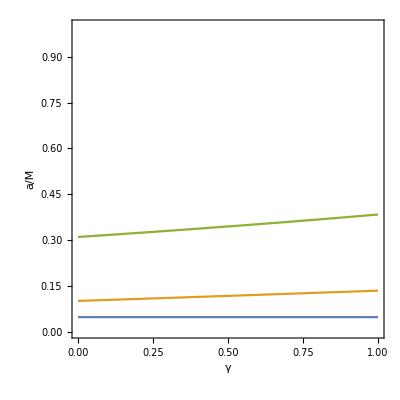

FindRoot::nlnum: The function value {-0.355347 (-1. ω+0.000130657 √(Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+«1»))-(42839.6 (1.70714×10^-8 (2.29771×10^9 Power[«2»]+1.51165×10^7 Plus[«2»]+46656. Plus[«2»]+«5»+216. Plus[«3»]+3240. Plus[«3»]+27. Plus[«4»])-«22» («1»)))/(√(1.08839×10^9 ω^2+1.00777×10^7 (1.+Times[«2»])+46656. (1.+Times[«2»])+«6»+324. (1.+Times[«2»]+Times[«2»])+3888. (2.4+Times[«2»]+Times[«2»])+«1»))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,0.5,0.4,ω]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.355347 (-1. ω+0.000130657 √(Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+«1»))-(42839.6 (1.70714×10^-8 (2.29771×10^9 Power[«2»]+1.51165×10^7 Plus[«2»]+46656. Plus[«2»]+«5»+216. Plus[«3»]+3240. Plus[«3»]+27. Plus[«4»])-«22» («1»)))/(√(1.08839×10^9 ω^2+1.00777×10^7 (1.+Times[«2»])+46656. (1.+Times[«2»])+«6»+324. (1.+Times[«2»]+Times[«2»])+3888. (2.4+Times[«2»]+Times[«2»])+«1»))} is not a list of numbers with dimensions {1} at {r} = {6.}.

ReplaceAll::reps: {FindRoot[∂_r k[r,0.5,0.4,ω]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

FindRoot::nlnum: The function value {-0.536489 (-1. ω+0.000131923 √(Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+Times[«2»]+«1»))-(40729.7 (1.74038×10^-8 (2.41865×10^9 Power[«2»]+1.51165×10^7 Plus[«2»]+«7»+5184. Plus[«3»]+69.12 Plus[«4»])-2.93237×10^-8 («1»)))/(√(1.16095×10^9 ω^2+1.00777×10^7 (1.+Times[«2»])+«8»+6220.8 (2.4+Times[«2»]+Times[«2»])+«1»))} is not a list of numbers with dimensions {1} at {r} = {6.}.

General::stop: Further output of FindRoot::nlnum will be suppressed during this calculation.

ReplaceAll::reps: {FindRoot[∂_r k[r,0.8,0.4,ω]==0,{r,6.}]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

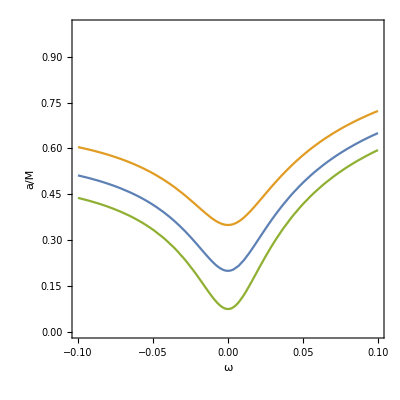

```mathematica
ContourPlot[{rk[a]-rr[Ω,0,0.01]==0,rk[a]-rr[Ω,0.4,0.01]==0,rk[a]-rr[Ω,0.8,0.01]==0,rk[a]-rr[Ω,0,-0.02]==0,rk[a]-rr[Ω,0.4,-0.02]==0,rk[a]-rr[Ω,0.8,-0.01]==0},{Ω,0,1},{a,0,1},Frame->True,FrameLabel->{"Ω","a/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15},PlotLegends->Placed[{"γ=0, ω=0.01","γ=0.4, ω=0.01","γ=0.8, ω=0.01","γ=0, ω=-0.01","γ=0.4, ω=-0.01","γ=0.8, ω=-0.01"},{Scaled[{0.05,0.15}],{-0.8,0.3}}],ContourStyle->{{Red},Blue, Green,{Dashed,Red},{Dashed,Blue},{Dashed, Green}}]

ContourPlot[{rk[a]==rr[0,γ,0.01],rk[a]==rr[0.3,γ,0],rk[a]==rr[0.6,γ,0.02]},{γ,0,1},{a,0,1},Frame->True,FrameLabel->{"γ","a/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15}]

ContourPlot[{rk[a]==rr[0.5,0.4,ω],rk[a]==rr[0.8,0.4,ω],rk[a]==rr[0.2,0.4,ω]},{ω,-0.1,0.1},{a,0,1},Frame->True,FrameLabel->{"ω","a/M"},LabelStyle->{FontFamily -> "Times",Black, Italic,FontSize-> 15}]
```